## 引言

庞大而复杂的Mathematica系统是在少数几条基本理念或者说原则上建立起来的。了解一下这些基本理念对后面的内容有帮助，下面做简要介绍。

## 万物皆为表达式

Mathematica中的所有东西都被当作表达式（expression）看待，表达式可以粗略地分为两种：原子（atom）和普通表达式（nomal expression）。

### 原子

原子顾名思义就是组成表达式的最小成分，原子可按照以下方法分类：

数字（numbers）

Real（实数，如3.22）

Rational（分数，如Rational[2,3])

Complex（复数，如1+2I）

Symbol(符号,如Pi,Plot,a,b)

String(字符串，如"Mathematica is a new way of thinking!")

在现实世界中，原子构筑起大千世界；在Mathematica中，原子组成所有的普通表达式。内置函数AtomQ可以用来测试一个表达式是否为原子：

```mathematica
ClearAll["Global`*"];
{AtomQ[x],AtomQ[Sin[x]],AtomQ[1+I*2],AtomQ[2/3]}
```

{True,False,True,True}

### 普通表达式

上面提到，普通表达式是由原子构成的，构成的一般格式是：expr[expr1,expr2,...,exprn]。<expr>称为头部（head),它本身可以是一个普通表达式而不一定是原子[1]。头部后面跟上一对方括号，可以姑且理解为其它编程语言中的函数参数的标识，比如C语言中的小括号。< expr1,expr2,...,exprn >是此表达式的成员（elements,可以理解为C中的函数参数），成员的个数可以为任意个，包括0个。表达式的头部和成员本身可以是不可再细分的原子，也可以是由相同的格式构成的子表达式。可以把一个普通表达式看成树一样的结构，树叶（原子）构成树枝（子表达式）,树枝再构成树干。

### 内置函数的等价形式 FullForm命令

上面的提到的头部加元素这种构成格式是Mathematica的通用表示方法，内核中的计算都是按照这种形式进行的。但是为了方便用户的输入和阅读，对于一些常用的函数，Mathematica提供了较为简洁等价形式。例如1加1的完全形式是Plus[1,1],这真是麻烦啊，直接写1+1就可以了。对于常见的数学运算，基本上都可以用标准的数学符号简写，+、-、*、\、^等等。 有时需要查看一个表达式的完全形式，这就要用到函数FullForm：

```mathematica
FullForm[x*Sin[a+b]]
```

Times[x,Sin[Plus[a,b]]]

### 表达式的索引

可以使用索引（Part命令）来访问一个表达式的内部（方括号里面的部分）。下面举例：

```mathematica
expr=x*Sin[a+b];{expr[[0]],expr[[1]],expr[[2]],expr[[2,1]],expr[[2,1,1]]}
```

{Times,x,Sin[a+b],a+b,a}

可以看到，索引值0代表表达式的头部（f[[0]]相当于Head[f])，索引值1、2、3分别代表表达式的第1、2、3个元素。逗号可以用来进行多层访问。用这种方法我们可以对任意表达式进行重组和改变。

```mathematica
Level[expr,{3}]
```

{a,b}

可用TreeForm查看expr的树形结构以直观表示此Level的功能，命令为TreeForm[expr]:

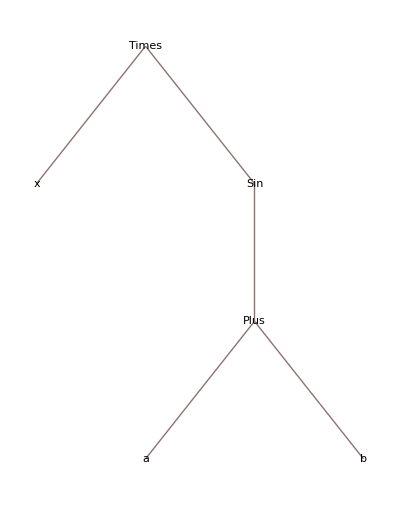

```mathematica
TreeForm[expr]
```

Level的第二个参数的常见用法有：

Level[ex,n]：显示1到n层的子表达式

Level[ex,{n}]：只显示第n层的子表达式

Level[ex,{-n}]：显示倒数第n层的子表达式

这种表示层次的方法在Mathematica中是通用的，很多的内置函数都采用此方法指明层次。具体用法请详见帮助。

## 模式匹配与规则替换

Mathematica中还有一个非常基本的概念，这就是模式匹配(pattern-matching），模式匹配是一个将规则与表达式对应起来的系统。一切功能都建立在模式匹配上，没有了它，Mathematica不知道对表达式进行何种操作。模式匹配更侧重于匹配表达式的结构而不是语义，也就是说它更关注的是表达式的结构是怎么样的而不是表达式能干什么。

### 规则重写

一个典型的规则(rule),其中a和b都是某Mathematica表达式：

```mathematica
a->b
```

这条规则的意思是：每当碰到<a>的时候就把它替换为<b>。比如：

```mathematica
{a,c,d,c}/.a->b (*符号<expr/.rule>的意思是对表达式expr应用规则rule*)
```

{b,c,d,c}

一个模式是某些部分被替换为“空白”(“_”,完整形式为Blank[])的表达式，简单来说，这里的所谓的“空白”就是一个能代表任意表达式的占位符。比方说，f[x_]就表示f[anything]。

### 一个用模式定义的简单函数

```mathematica
Clear[f];
f[x_]:=x^2;
{f[2],f["word"],f[Newton]}
```

{4,word^2,Newton^2}

### 函数的本质是规则：DownValues命令

可以用内置的DownValues命令来查看规则的内部形式。我们在刚才定义的<f>身上试试看：

```mathematica
DownValues[f]
```

{HoldPattern[f[x_]]:>x^2}

这里出现的HoldPattern我们稍后讨论。形如x_的模式是最简单的模式，同时也有更多复杂的模式。有的模式还附带了条件（condition）,只有在满足条件的情况下才匹配。预知详情，请往后看。

### 基于限制模式的函数

现在举个例子：我们对前面定义的f加以限制，让它只能作用于整数。

```mathematica
Clear[f];
f[x_Integer]:=x^2;
{f[2],f[Pi],f["word"],f[Newton]}
```

{4,f[π],f[word],f[Newton]}

在这个例子里，我们引入了一个更复杂的模式:x_Integer。

### 浅议计算

通过上面的例子可以看到，对于一个表达式，如果没有一条规则的模式（箭头左边的项）与其匹配，那么Mathematica将会把它原样返回。这触及到Mathematica的核心计算方法：

接受一个输入内核的表达式

规则库（存放所有的系统规则和用户自定义规则的地方）里的所有规则都被应用到这个表达式

如果发现某个规则的模式与这个表达式匹配，立即运用此规则并将表达式重写并返回结果

循环地重复这个过程

有时，没有一条规则能匹配这个表达式。这个表达式就保持原有状态并返回。因为规则库里既有系统规则也有用户自定义规则，这给表达式的操纵带来极大的灵活性。

### 一个拥有多重定义的函数

现在定义一个新函数，这个函数对偶数进行线性计算，对奇数进行平方计算，对既不是奇数又不是偶数的数应用正弦函数（Sin）：

```mathematica
Clear[f];
f[x_?EvenQ]:=x;
f[x_?OddQ]:=x^2;
f[x_]:=Sin[x];
```

试试给它不同类型的参数：

```mathematica
{f[1],f[2],f[3],f[4],f[3/2],f[Newton],f[Pi]}
```

{1,2,9,4,Sin[3/2],Sin[Newton],0}

顺便说下，OddQ和EvenQ[5]是用来判断奇偶性的内置函数,用法从字面应该很容易看出来。

### 替换规则的顺序很重要

我们来看看上面<f>的第三个定义，f[x_] :=Sin[x] 。即无论遇到什么输入都计算其正弦。有的同学可能天真地据此认为上面代码的结果会是一堆Sin，不幸的是，因为替换规则的应用是有序（一个接着一个）的，我们没有得到一堆Sin。

首先，如果某次尝试中一个规则正好与表达式相匹配，那么计算就会马上进行，剩下的规则也就不会再尝试了；其次，如果有多条规则与一个表达式相匹配，应用在表达式上的第一条规则早已重写的该表达式从而使其他的几条规则不再匹配。

所以，最后的结果取决于尝试规则的顺序——Mathematica把规则库中的规则一个接着一个地应用在表达式上，遇到一个“合适”的便不再尝试。这就好比一个女神在一大堆男性仰慕者中找对象，她按照先来后到的顺序把这群男士排成对，然后一个接着一个的相亲，一旦遇上哪个高富帅符合她的标准就立马收手，当天成亲！剩下的不管是高富帅还是穷屌丝都直接轰走。

回到我们的<f>中来，f[x_] := Sin[x]是在最后定义的，所以对于奇数或偶数的参数来说，Sin[x]是根本没有机会的！

### 规则的自动重排

看起来定义规则的顺序对最后的结果十分重要，那我们已不是要处处小心定义的顺序吗？其实，Mathematica足够聪明，对于一些简单的情况它是能自动区别优先级的。比方说对于上面的那个例子，就算我们把f[x_]:=Sin[x]放在第一个定义，结果还是不会变。因为Mathematica能够自动重排规则。

```mathematica
Clear[f];
f[x_]:=Sin[x];
f[x_?EvenQ]:=x;
f[x_?OddQ]:=x^2;
{f[1],f[2],f[3],f[4],f[3/2],f[Newton]}
```

{1,2,9,4,Sin[3/2],Sin[Newton]}

用DownValues瞧瞧定义在<f>上的规则是怎么排列的：

```mathematica
DownValues[f]
```

{HoldPattern[f[x_?EvenQ]]:>x,HoldPattern[f[x_?OddQ]]:>x^2,HoldPattern[f[x_]]:>Sin[x]}

喏，Mathematica很聪明吧！Sin那条规则又被排到了最后，虽然它是最先定义的。Mathematica内置了一个“规则分析器”，这东西会尽量（是的，它尽力了）在把普遍规则挪到特殊规则后面。当然了，这一招不会总是奏效，有时也会不尽人意，应当小心一点。事实上，需要你手动更改规则顺序的情况是及其少见的。

### 表达式的计算

上个例子引入了第三个原则：表达式的计算和规则重写。其实讲的就是一个Mathematica计算到底是怎么完成的。这个前面也提到过一点，这里用通俗的语言进行描述：当你在笔记本中输入任意一个表达式并按下shift+enter，这个表达式就被送入内核中计算。接下来Mathematica就在全局规则库中找能与这个表达式相匹配的替换规则（形如object1->object2)。如果找到了，这个表达式或者它的子表达式就被重写，然后这个过程从头开始。这个过程会一直循环下去直到全局规则库中找不出与之匹配的规则。这时的表达式（被重写n次）就被当作最后的结果输出了。

全局规则库里包含了系统内置的规则和用户自定义规则。通常用户自定义的规则优先级要高一点[7]。实际上，所有的变量赋值、函数定义都是通过存储在全局规则库中的某种规则实现的。也就是说，函数和变量之间没有本质的区别，They are just rules！

举个例子：

```mathematica
FullForm[Sin[Pi+Pi]]
```

0

什么？您期待的结果是Sin[Plus[Pi,Pi]]？这是因为规则库中有类似于Plus[x_,x_]->2 x和Sin[2 Pi]->0的规则，又因为默认的计算顺序是从表达式的内层开始的，所以等到FullForm大显身手的时候Sin[Pi+Pi]已经被重写为0了。用内置函数Trace可以监视表达式的技术过程：

```mathematica
Trace[FullForm[Sin[Pi+Pi]]]
```

{{{π+π,2 π},Sin[2 π],0},0}

### 总结

我们简要的说明了Mathematica的核心理念，同时也介绍了一些内置函数：AtomQ、Head、FullForm、TreeForm、Level、Plus、Times、Trace、DownValues、OddQ、EvenQ。